```mathematica
SetDirectory[NotebookDirectory[]];
data = SemanticImport["CoeffDataPurified.csv"];
TBckg = 80;
row =Position[data[All,"T"], TBckg];
row = Flatten[row];

d=2;
kappa = Extract[data[All, "kp"], row] + Extract[data[All, "kc"], row];
HeatCapacity = 10^12*Extract[data[All, "C"], row];
DiffScatter = 10^9*Extract[data[All, "D"], row];
W = 10^3*Extract[data[All, "W"], row];
A = 10^6*Extract[data[All, "A"], row];
mu1 = Extract[data[All, "mu1"], row];
mu2 = Extract[data[All, "mu2"], row];
mu3 = Extract[data[All, "mu3"], row];

L = 1*^-6;
τ = 1*^-9;
URef = 1;
TRef =1;
β = kappa/HeatCapacity;
tHeat = 0.4*^-9;
τHeat = tHeat/τ;
σx = 2*^-6;
σy=2.8*^-6;
xc = 5*^-6;
Σx = σx/L;
Σy = σy/L;
Xc = xc/L;
H = 200*0.013*10^18;
HH = τ/(TRef*HeatCapacity)H;
Pi1 =β*τ/L^2;
Pi21 = τ*mu1/A/L^2;
Pi22 = τ*mu2/A/L^2;
Pi23 = τ*mu3/A/L^2;
Pi3 = DiffScatter*τ;
Pi4 = (W*τ)/(L*TRef)*Sqrt[(TBckg*A)/HeatCapacity];
Pi5 = (W*τ*TRef)/(L*URef)*Sqrt[HeatCapacity/(A*TBckg) ];
Pi2 = Table[(Pi21-Pi22-Pi23)*KroneckerDelta[i,j]*KroneckerDelta[j,k]*KroneckerDelta[k,l] + Pi22*KroneckerDelta[i,k]*KroneckerDelta[j,l] + Pi23*KroneckerDelta[i,l]*KroneckerDelta[j,k],{i,d},{j,d}, {k,d}, {l,d}];
SpatCoords=Table[Subscript[x,i],{i,d}];
```

```mathematica
eqn1 = D[T[Subscript[x, 1],Subscript[x, 2],t],t] + Pi4*Sum[D[Subscript[u, i][Subscript[x, 1],Subscript[x, 2],t],Part[SpatCoords,i] ],{i,1,d}]-Pi1*Sum[D[T[Subscript[x, 1],Subscript[x, 2],t],Part[SpatCoords,i],Part[SpatCoords,i]]  ,{i,1,d}]==HH*HeavisideTheta[τHeat-t]*Exp[-(Subscript[x, 1]+Xc)^2/(2*Σx^2)-Subscript[x, 2]^2/(2*Σy^2)];
eqn2 = D[Subscript[u, 1][Subscript[x, 1],Subscript[x, 2],t], t] + Pi5*D[T[Subscript[x, 1],Subscript[x, 2],t],Part[SpatCoords,1]]- Sum[D[Subscript[u, k][Subscript[x, 1],Subscript[x, 2],t],Part[SpatCoords,j],Part[SpatCoords,l]]*Part[Pi2,1,j,k,l],{j,1,d},{k,1,d},{l,1,d} ]+ Pi3*Subscript[u, 1][Subscript[x, 1],Subscript[x, 2],t]==0;
eqn3 = D[Subscript[u, 2][Subscript[x, 1],Subscript[x, 2],t], t] + Pi5*D[T[Subscript[x, 1],Subscript[x, 2],t],Part[SpatCoords,2]]- Sum[D[Subscript[u, k][Subscript[x, 1],Subscript[x, 2],t],Part[SpatCoords,j],Part[SpatCoords,l]]*Part[Pi2,2,j,k,l],{j,1,d},{k,1,d},{l,1,d} ]+ Pi3*Subscript[u, 2][Subscript[x, 1],Subscript[x, 2],t]==0;
eqn1 =eqn1 /.{Subscript[u,1]->u, Subscript[u,2]->v, Subscript[x,1]->x, Subscript[x,2]->y}
eqn2 =eqn2 /.{Subscript[u,1]->u, Subscript[u,2]->v, Subscript[x,1]->x, Subscript[x,2]->y}
eqn3 =eqn3 /.{Subscript[u,1]->u, Subscript[u,2]->v, Subscript[x,1]->x, Subscript[x,2]->y}
```

T^(0,0,1)[x,y,t]+0.0419729 (v^(0,1,0)[x,y,t]+u^(1,0,0)[x,y,t])-0.118984 (T^(0,2,0)[x,y,t]+T^(2,0,0)[x,y,t])==11.2556 ⅇ^(-1/8 (5+x)^2-0.0637755 y^2) HeavisideTheta[0.4-t]

0.+0.168503 u[x,y,t]+u^(0,0,1)[x,y,t]-0.00152916 u^(0,2,0)[x,y,t]+285.097 T^(1,0,0)[x,y,t]-0.000541983 v^(1,1,0)[x,y,t]-0.00263026 u^(2,0,0)[x,y,t]==0

0.+0.168503 v[x,y,t]+v^(0,0,1)[x,y,t]+285.097 T^(0,1,0)[x,y,t]-0.00263026 v^(0,2,0)[x,y,t]-0.000541983 u^(1,1,0)[x,y,t]-0.00152916 v^(2,0,0)[x,y,t]==0

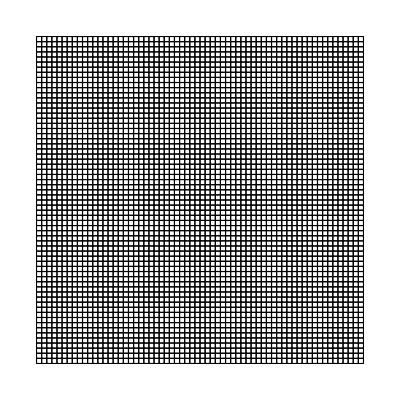

```mathematica
Needs["NDSolve`FEM`"];
DomainLen =10;
tMax = 5;
Ω=ImplicitRegion[True,{x,y}];
mesh=ToElementMesh[Ω,{{-DomainLen,DomainLen},{-DomainLen,DomainLen}},"MaxCellMeasure"->DomainLen/100];
mesh["Wireframe"]
```

```mathematica
BCT = DirichletCondition[T[x,y,t]==0, True];
BCU1 = DirichletCondition[u[x,y,t] ==0, True];
BCU2 = DirichletCondition[v[x,y,t] ==0, True];
ICT = T[x,y,0] == 0;
ICU1 = u[x,y,0] == 0;
ICU2 = v[x,y,0] == 0;
```

```mathematica
usol=NDSolve[{eqn1, eqn2, eqn3, ICT, ICU1, ICU2,BCT,  BCU1, BCU2},{T, u,v}, {t, 0, tMax}, {x, y}∈mesh, Method->{"PDEDiscretization"->{"MethodOfLines","SpatialDiscretization"->{"FiniteElement"}}}]
```

{{T→InterpolatingFunction[{{-10., 10.}, {-10., 10.}, {0., 5.}}, <>],u→InterpolatingFunction[{{-10., 10.}, {-10., 10.}, {0., 5.}}, <>],v→InterpolatingFunction[{{-10., 10.}, {-10., 10.}, {0., 5.}}, <>]}}

```mathematica
tVis =4.6;
(*MaxT =Max[Table[T[x,y, t]/.usol, {x,-DomainLen,DomainLen},{y,-DomainLen,DomainLen}, {t,0,tMax} ]]
MinT =Min[Table[T[x,y, t]/.usol, {x,-DomainLen,DomainLen},{y,-DomainLen,DomainLen}, {t,0,tMax}]]*)
(*Plot3D[TBckg+TRef*T[x,y, tVis]/.usol, {x,-DomainLen,DomainLen},{y,-DomainLen,DomainLen}, PlotRange->{{-10,10},{-10,10},{TBckg+TRef*MinT,TBckg+4*TRef*MaxT}}]*)
Plot3D[TBckg+TRef*T[x,y, tVis]/.usol, {x,-DomainLen,DomainLen},{y,-DomainLen,DomainLen}, PlotRange->{{-10,10},{-10,10},{78,82}}]
(*VectorDensityPlot[{{ u[x,y,tVis]/.usol, v[x,y,tVis]/.usol}, T[x,y,tVis]/.usol},{x,-DomainLen,DomainLen},{y,-DomainLen,DomainLen}, PlotLegends->Automatic, ColorFunction->"TemperatureMap",VectorRange->All]*)
```

-Graphics3D-

```mathematica
Manipulate[Plot[TBckg+TRef*T[x,0, t]/.usol, {x, -DomainLen, DomainLen}], {t, 0, tMax}]
(*Table[T[x,0, 0.285]/.usol, {x, -DomainLen, DomainLen}]
Table[u[x,0, 0.285]/.usol, {x, -DomainLen, DomainLen}]
T[0,0, 1]/.usol*)
```

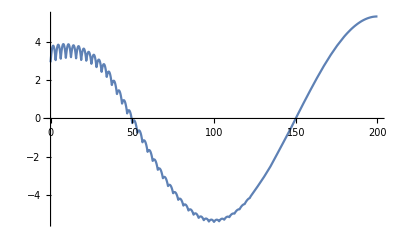

```mathematica
Plot[T[x,DomainLen/2, 1]/.usol, {x, 0, DomainLen}, PlotRange->All]
```

```mathematica
TBckg
```

80

```mathematica
TRef
```

80